```mathematica
X0=RandomVariate[UniformDistribution[{0,π/2}],10^5]
```

```mathematica
X = Tan[X0]
```

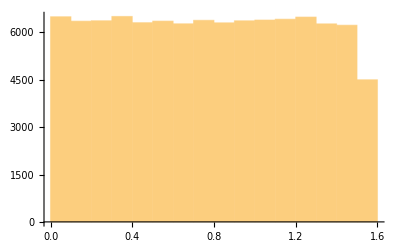

```mathematica
Histogram[X0]
```

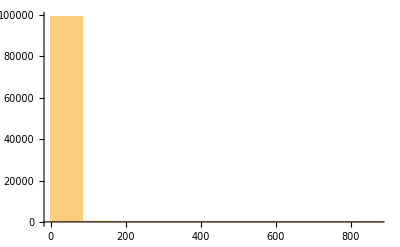

```mathematica
Histogram[X]
```

## M-S Plot for p = 1

```mathematica
MP[X_,p_,n_]:= Max[Table[Abs[X[[i]]]^p,{i,1,n}]]/(∑_(i=1)^n (Abs[X[[i]]]^p));
taMean = Table[{n, MP[X,1,n]},{n,1,200}];
```

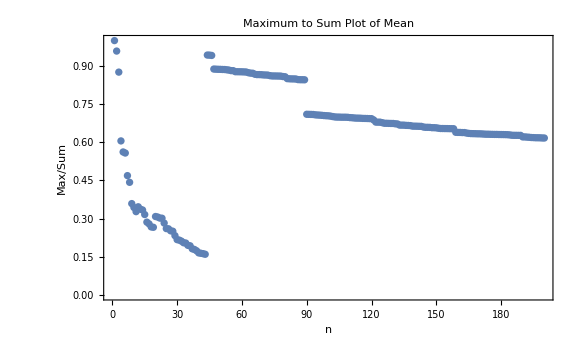

```mathematica
ListPlot[taMean,Frame->True,FrameLabel->{"n","Max/Sum"},PlotLabel->"Maximum to Sum Plot of Mean", ImageSize->Large]
```

## M-S Plot for p = 2

```mathematica
MP[X_,p_,n_]:= Max[Table[Abs[X[[i]]]^p,{i,1,n}]]/(∑_(i=1)^n (Abs[X[[i]]]^p));
taVar = Table[{n, MP[X,2,n]},{n,1,200}];
```

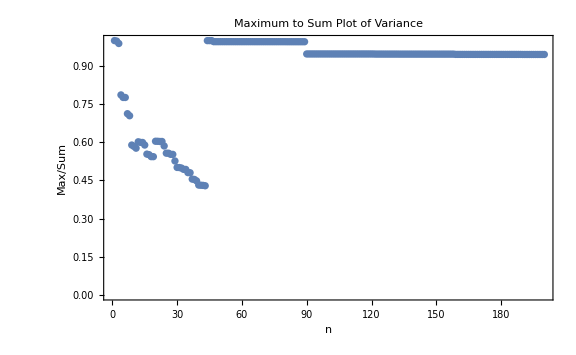

```mathematica
ListPlot[taVar,Frame->True,FrameLabel->{"n","Max/Sum"},PlotLabel->"Maximum to Sum Plot of Variance", ImageSize->Large]
```